# Unfinished examples

## Unfinished Interferometry Example

```mathematica
(*1. Curvature V2(t):Harmonic (1/2)->Inverted Barrier (-1/2) on[2,4]->Harmonic (1/2)*)v2Interferometer[t_]:=(1/2)-(1/2)*(Tanh[4*(t-2)]-Tanh[4*(t-4)]);

(*2. Weak Linear Tilt V1(t) applied ONLY while the arms are separated (around t=4.5)*)
v1Tilt[f0_][t_]:=-f0*Exp[-(t-4.5)^2/0.8^2];

(*3. Initialize First Excited HO State Approximation (Antisymmetric:"C"->-1,x0=+/-0.25)*)
tMin=0;tMax=10;
x0Split=0.25;

(*Unperturbed Reference Interferometer (f0=0) vs.Tilted Interferometer (f0=0.35)*)
intRef=GWP["SS1D"][{1/2,1/2},{-x0Split,x0Split},{0,0},{0,0},"C"->-1,"Potential"->{"Numerical",0&,v1Tilt[0.0],v2Interferometer,tMin,tMax}];

intTilt=GWP["SS1D"][{1/2,1/2},{-x0Split,x0Split},{0,0},{0,0},"C"->-1,"Potential"->{"Numerical",0&,v1Tilt[0.35],v2Interferometer,tMin,tMax}];
```

```mathematica
Plot3D[v1Tilt[2][t]x+v2Interferometer[t]*x^2,{t,0,2Pi},{x,-5,5}]
```

-Graphics3D-

```mathematica
rhoRef=intRef["RHOX"];
rhoTilt=intTilt["RHOX"];
DensityPlot[rhoRef[x,t],{t,tMin,tMax},{x,-15,15},PlotPoints->50]
DensityPlot[rhoTilt[x,t],{t,tMin,tMax},{x,-15,15},PlotPoints->50]
```

```mathematica
Plot[{rhoRef[x,6.25],rhoTilt[x,6.25]},{x,-10,10},PlotRange->All]
Plot[{rhoRef[x,6],rhoTilt[x,6]},{x,-10,10}]
```

## Perfect mode coupling

In this follow up example

```mathematica
(*Clear memoized NDSolve trajectories before re-evaluating*)
GWPClearCache[];

(*Symbolic pi-swap coupling formula as a function of window duration dt=t2-t1 and ramp slope s*)
kappaSwap[dt_,s_]:=(Pi/dt)*Sqrt[1-(Pi/(2*dt))^2]+(3*Pi^3)/(16*s*dt^4)+(Pi^5*(162-41*s*dt))/(1536*s^2*dt^7);

(*Parameters*)
tMin=-20;
tMax=70;
t1=10;
t2=35;
s=1/2; (*Gentler ramp slope s=1/2 suppresses non-adiabatic turn-on kick*)

v00=0&;v10=0&;v01=0&;
v20Func=(1/2)&;v02Func=(1/2)&;

(*Exact symbolic kappaXY for the chosen (t1,t2,s)*)
kappaXY=kappaSwap[t2-t1,s];
v11Window[t_]:=kappaXY*(1/2)*(Tanh[s*(t-t1)]-Tanh[s*(t-t2)]);

(*Initial state:squeezed+displaced along x,ground state along y*)
aMat0={{1,0},{0,1/2}};
r0={3/2,0};
p0={0,0};
psi2D=GWP["2D"][aMat0,r0,p0,0,"Potential"->{"Numerical",v00,v10,v01,v20Func,v02Func,v11Window,tMin,tMax,AccuracyGoal->12,PrecisionGoal->12}];
```

Cleared memoized NDSolve caches for: {MaddoxScience`GWPTools`GWPDeveloper`GWP1DNDSolveCache,MaddoxScience`GWPTools`GWPDeveloper`GWP2DNDSolveCache,MaddoxScience`GWPTools`GWPDeveloper`GWPMC1DNDSolveCache,MaddoxScience`GWPTools`GWPDeveloper`GWPRDM1DNDSolveCache,MaddoxScience`GWPTools`GWPDeveloper`GWPSS1DNDSolveCache}

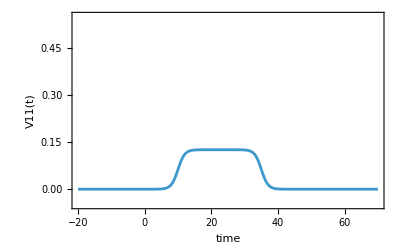

```mathematica
(*Visualize the bilinear mode-coupling window V11(t)*)
Plot[v11Window[t],{t,tMin,tMax},PlotRange->{-0.05,0.55},Frame->True,FrameLabel->{"time","V11(t)"},BaseStyle->FontSize->12]
```

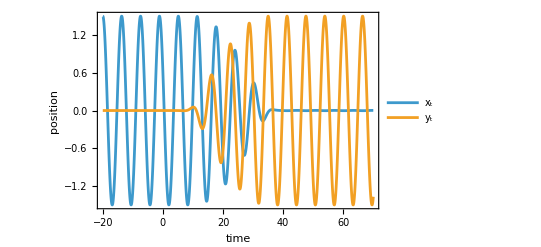

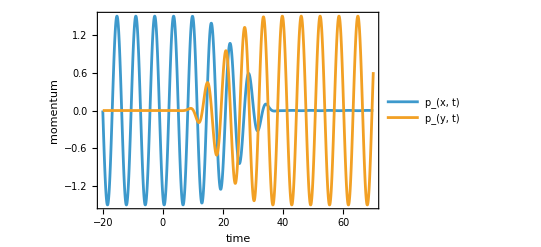

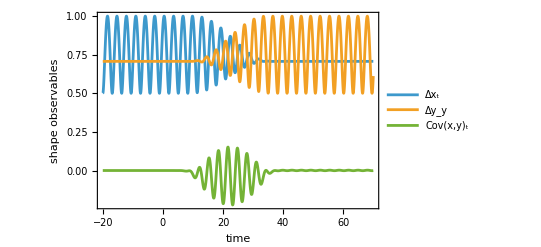

```mathematica
opts={Frame->True,BaseStyle->FontSize->12};
Plot[{
psi2D["PositionCenterX"][t],
psi2D["PositionCenterY"][t]},{t,tMin,tMax},Evaluate@opts,PlotLegends->{"x_t","y_t"},FrameLabel->{"time","position"}]
Plot[{
psi2D["MomentumCenterX"][t],
psi2D["MomentumCenterY"][t]},{t,tMin,tMax},Evaluate@opts,PlotLegends->{"p_(x, t)","p_(y, t)"},FrameLabel->{"time","momentum"}]
Plot[{
psi2D["PositionUncertaintyX"][t],
psi2D["PositionUncertaintyY"][t],
psi2D["PositionCovarianceXY"][t]},{t,tMin,tMax},Evaluate@opts,PlotLegends->{"Δx_t","Δy_y","Cov(x,y)_t"},FrameLabel->{"time","shape observables"}]
```